```mathematica
Total[TensorProduct[#,#]&/@{{1,1,0},{1,-1,0},{-1,1,0},{-1,-1,0},{0,0,1},{0,0,-1}}]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Tuples[{-1,1},3]
```

{{-1,-1,-1},{-1,-1,1},{-1,1,-1},{-1,1,1},{1,-1,-1},{1,-1,1},{1,1,-1},{1,1,1}}

```mathematica
Total[3/(8(√3)^2)TensorProduct[#,#]&/@Tuples[{-1,1},3]]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
Total[1/3 TensorProduct[#,#]&/@{{0,1},{(√3)/2,1/2},{(√3)/2,-1/2},{0,-1},{-(√3)/2,-1/2},{-(√3)/2,1/2}}]
```

{{1,0},{0,1}}

```mathematica
ul=Block[{q=5},(2*Range[q]-q-1)/(2*q)]
```

{-2/5,-1/5,0,1/5,2/5}

```mathematica
pts=Flatten[Table[j*{0,1}+i*{(√3)/2,-1/2},{i,ul},{j,ul}],1]//N
```

{{-0.34641,-0.2},{-0.34641,0.},{-0.34641,0.2},{-0.34641,0.4},{-0.34641,0.6},{-0.173205,-0.3},{-0.173205,-0.1},{-0.173205,0.1},{-0.173205,0.3},{-0.173205,0.5},{0.,-0.4},{0.,-0.2},{0.,0.},{0.,0.2},{0.,0.4},{0.173205,-0.5},{0.173205,-0.3},{0.173205,-0.1},{0.173205,0.1},{0.173205,0.3},{0.34641,-0.6},{0.34641,-0.4},{0.34641,-0.2},{0.34641,0.},{0.34641,0.2}}

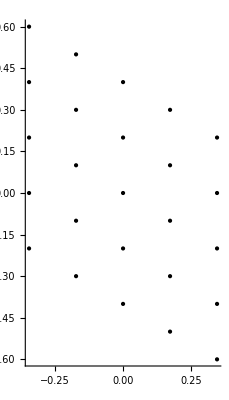

```mathematica
Graphics[Point[pts],Axes->True]
```

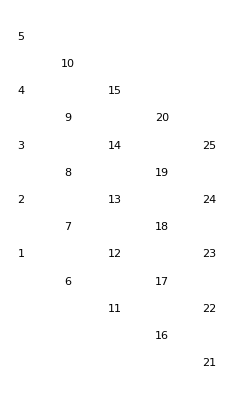

```mathematica
Graphics[MapThread[Text[ToString@#1,#2]&,{Range[25],pts}]]
```

```mathematica
Graphics[Point[pts],Axes->True]
```

-Graphics-